# Day 12

# Day12

```mathematica
i=0;
elevationMap = Association@@Function[
i++;
# -> i
] /@ CharacterRange["a", "z"];
elevationMap["S"] = 1;
elevationMap["E"] = 26;
elevationMap
```

<|a→1,b→2,c→3,d→4,e→5,f→6,g→7,h→8,i→9,j→10,k→11,l→12,m→13,n→14,o→15,p→16,q→17,r→18,s→19,t→20,u→21,v→22,w→23,x→24,y→25,z→26,S→1,E→26|>

```mathematica
testInput = "Sabqponm
abcryxxl
accszExk
acctuvwj
abdefghi";
```

```mathematica
testInputParsed =Function[
Characters[#] 
] /@ StringSplit[testInput, "\n"]
```

{{S,a,b,q,p,o,n,m},{a,b,c,r,y,x,x,l},{a,c,c,s,z,E,x,k},{a,c,c,t,u,v,w,j},{a,b,d,e,f,g,h,i}}

```mathematica
posToValueTest = Association@@
Flatten@MapIndexed[
Function[{row, rindex},
	 MapIndexed[
	Function[{column, cindex},
	{rindex[[1]], cindex[[1]]} ->  testInputParsed[[rindex[[1]], cindex[[1]]]]
	],
	row
	]
],
	testInputParsed
]
```

<|{1,1}→S,{1,2}→a,{1,3}→b,{1,4}→q,{1,5}→p,{1,6}→o,{1,7}→n,{1,8}→m,{2,1}→a,{2,2}→b,{2,3}→c,{2,4}→r,{2,5}→y,{2,6}→x,{2,7}→x,{2,8}→l,{3,1}→a,{3,2}→c,{3,3}→c,{3,4}→s,{3,5}→z,{3,6}→E,{3,7}→x,{3,8}→k,{4,1}→a,{4,2}→c,{4,3}→c,{4,4}→t,{4,5}→u,{4,6}→v,{4,7}→w,{4,8}→j,{5,1}→a,{5,2}→b,{5,3}→d,{5,4}→e,{5,5}→f,{5,6}→g,{5,7}→h,{5,8}→i|>

```mathematica
Select[posToValue, # == "S" &]
```

<|{1,1}→S|>

```mathematica
graphPathsTest = Module[{rowMax, columnMax, tag, col, r, currentValue, neighbor},
rowMax = Echo@ Length[testInputParsed];
columnMax = Echo@ Length[testInputParsed[[1]]];
ReapList[
tag,
MapIndexed[
Function[{row, rindex},
	MapIndexed[
	Function[{column, cindex},
		col = cindex[[1]];
		r = rindex[[1]];
		currentValue = posToValueTest[{r, col}];
		(* Left *)
		If [col > 1,
			neighbor = posToValueTest[{r, col -1}];
			If [Or[
					elevationMap[currentValue] + 1 ≥ elevationMap[neighbor],
					elevationMap[currentValue] > elevationMap[neighbor]
				],
				Sow[{currentValue, r, col} -> {neighbor, r, col-1}, tag]
			]
		];
		
		(* Right *)
		If [col < columnMax,
			neighbor = posToValueTest[{r, col +1}];
			If [Or[
					elevationMap[currentValue] + 1 ≥ elevationMap[neighbor],
					elevationMap[currentValue] > elevationMap[neighbor]
				],
				Sow[{currentValue, r, col} -> {neighbor, r, col+1}, tag]
			]
		];
		
		(* Up *)
		If [r > 1,
			neighbor = posToValueTest[{r-1, col}];
			If [Or[
					elevationMap[currentValue] + 1 ≥ elevationMap[neighbor],
					elevationMap[currentValue] > elevationMap[neighbor]
				],
				Sow[{currentValue, r, col} -> {neighbor, r-1, col}, tag]
			]
		];
		
		(* Down *)
		If [r < rowMax,
			neighbor = posToValueTest[{r+ 1, col}];
			If [Or[
					elevationMap[currentValue] + 1 ≥ elevationMap[neighbor],
					elevationMap[currentValue] > elevationMap[neighbor]
				],
				Sow[{currentValue, r, col} -> {neighbor, r+1, col}, tag]
			]
		];
		
	],
	row
	]
],
testInputParsed
]
]
];
DeleteDuplicates[graphPathsTest]
```

5

8

{{S,1,1}→{a,1,2},{S,1,1}→{a,2,1},{a,1,2}→{S,1,1},{a,1,2}→{b,1,3},{a,1,2}→{b,2,2},{b,1,3}→{a,1,2},{b,1,3}→{c,2,3},{q,1,4}→{b,1,3},{q,1,4}→{p,1,5},{q,1,4}→{r,2,4},{p,1,5}→{q,1,4},{p,1,5}→{o,1,6},{o,1,6}→{p,1,5},{o,1,6}→{n,1,7},{n,1,7}→{o,1,6},{n,1,7}→{m,1,8},{m,1,8}→{n,1,7},{m,1,8}→{l,2,8},{a,2,1}→{b,2,2},{a,2,1}→{S,1,1},{a,2,1}→{a,3,1},{b,2,2}→{a,2,1},{b,2,2}→{c,2,3},{b,2,2}→{a,1,2},{b,2,2}→{c,3,2},{c,2,3}→{b,2,2},{c,2,3}→{b,1,3},{c,2,3}→{c,3,3},{r,2,4}→{c,2,3},{r,2,4}→{q,1,4},{r,2,4}→{s,3,4},{y,2,5}→{r,2,4},{y,2,5}→{x,2,6},{y,2,5}→{p,1,5},{y,2,5}→{z,3,5},{x,2,6}→{y,2,5},{x,2,6}→{x,2,7},{x,2,6}→{o,1,6},{x,2,7}→{x,2,6},{x,2,7}→{l,2,8},{x,2,7}→{n,1,7},{x,2,7}→{x,3,7},{l,2,8}→{m,1,8},{l,2,8}→{k,3,8},{a,3,1}→{a,2,1},{a,3,1}→{a,4,1},{c,3,2}→{a,3,1},{c,3,2}→{c,3,3},{c,3,2}→{b,2,2},{c,3,2}→{c,4,2},{c,3,3}→{c,3,2},{c,3,3}→{c,2,3},{c,3,3}→{c,4,3},{s,3,4}→{c,3,3},{s,3,4}→{r,2,4},{s,3,4}→{t,4,4},{z,3,5}→{s,3,4},{z,3,5}→{E,3,6},{z,3,5}→{y,2,5},{z,3,5}→{u,4,5},{E,3,6}→{z,3,5},{E,3,6}→{x,3,7},{E,3,6}→{x,2,6},{E,3,6}→{v,4,6},{x,3,7}→{k,3,8},{x,3,7}→{x,2,7},{x,3,7}→{w,4,7},{k,3,8}→{l,2,8},{k,3,8}→{j,4,8},{a,4,1}→{a,3,1},{a,4,1}→{a,5,1},{c,4,2}→{a,4,1},{c,4,2}→{c,4,3},{c,4,2}→{c,3,2},{c,4,2}→{b,5,2},{c,4,3}→{c,4,2},{c,4,3}→{c,3,3},{c,4,3}→{d,5,3},{t,4,4}→{c,4,3},{t,4,4}→{u,4,5},{t,4,4}→{s,3,4},{t,4,4}→{e,5,4},{u,4,5}→{t,4,4},{u,4,5}→{v,4,6},{u,4,5}→{f,5,5},{v,4,6}→{u,4,5},{v,4,6}→{w,4,7},{v,4,6}→{g,5,6},{w,4,7}→{v,4,6},{w,4,7}→{j,4,8},{w,4,7}→{x,3,7},{w,4,7}→{h,5,7},{j,4,8}→{k,3,8},{j,4,8}→{i,5,8},{a,5,1}→{b,5,2},{a,5,1}→{a,4,1},{b,5,2}→{a,5,1},{b,5,2}→{c,4,2},{d,5,3}→{b,5,2},{d,5,3}→{e,5,4},{d,5,3}→{c,4,3},{e,5,4}→{d,5,3},{e,5,4}→{f,5,5},{f,5,5}→{e,5,4},{f,5,5}→{g,5,6},{g,5,6}→{f,5,5},{g,5,6}→{h,5,7},{h,5,7}→{g,5,6},{h,5,7}→{i,5,8},{i,5,8}→{h,5,7},{i,5,8}→{j,4,8}}

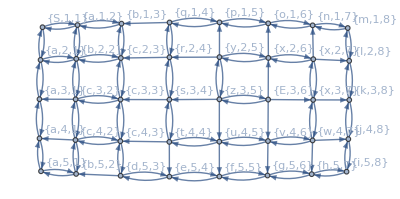

```mathematica
graphTest = Graph[graphPathsTest, VertexLabels->"Name"]
```

```mathematica
startPosTest =Keys[Select[posToValueTest, # == "S" &]][[1]];
startPosTest = Flatten@{"S", startPosTest};
endPosTest = Keys[Select[posToValueTest, # == "E" &]][[1]];
endPosTest = Flatten@{"E", endPosTest}
```

{E,3,6}

```mathematica
shortestPathTest =FindShortestPath[graphTest,startPosTest, endPosTest]
```

{{S,1,1},{a,1,2},{b,1,3},{c,2,3},{c,3,3},{c,4,3},{d,5,3},{e,5,4},{f,5,5},{g,5,6},{h,5,7},{i,5,8},{j,4,8},{k,3,8},{l,2,8},{m,1,8},{n,1,7},{o,1,6},{p,1,5},{q,1,4},{r,2,4},{s,3,4},{t,4,4},{u,4,5},{v,4,6},{w,4,7},{x,3,7},{x,2,7},{x,2,6},{y,2,5},{z,3,5},{E,3,6}}

```mathematica
Length[shortestPathTest] -1
```

31

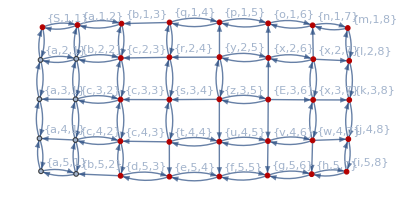

```mathematica
HighlightGraph[graphTest,PathGraph[shortestPathTest]]
```

## Real Data

```mathematica
i=0;
elevationMap = Association@@Function[
i++;
# -> i
] /@ CharacterRange["a", "z"];
elevationMap["S"] = 1;
elevationMap["E"] = 26;
elevationMap
```

<|a→1,b→2,c→3,d→4,e→5,f→6,g→7,h→8,i→9,j→10,k→11,l→12,m→13,n→14,o→15,p→16,q→17,r→18,s→19,t→20,u→21,v→22,w→23,x→24,y→25,z→26,S→1,E→26|>

```mathematica
data =Import["C:\\Users\\kylej\\Downloads\\input.txt"];
```

```mathematica
dataParsed =Function[
Characters[#] 
] /@ StringSplit[data, "\n"];
```

```mathematica
dataParsed//Length
dataParsed[[1]]//Length
```

41

163

```mathematica
posToValue = Association@@
Flatten[
	MapIndexed[
		Function[
			{row, rindex},
			MapIndexed[
				Function[
					{column, cindex},
					{
						rindex[[1]],
						cindex[[1]]
					} -> dataParsed[[rindex[[1]], cindex[[1]]]]
				],
				row
			]
		],
		dataParsed
	]
]
```

<|{1,1}→a,{1,2}→b,{1,3}→c,{1,4}→c,{1,5}→c,{1,6}→c,{1,7}→a,{1,8}→a,{1,9}→a,{1,10}→a,{1,11}→a,{1,12}→a,{1,13}→a,{1,14}→a,{1,15}→a,{1,16}→a,{1,17}→a,{1,18}→a,{1,19}→a,{1,20}→c,{1,21}→c,6641,{41,143}→c,{41,144}→c,{41,145}→c,{41,146}→c,{41,147}→c,{41,148}→c,{41,149}→c,{41,150}→c,{41,151}→c,{41,152}→c,{41,153}→c,{41,154}→c,{41,155}→c,{41,156}→c,{41,157}→c,{41,158}→a,{41,159}→a,{41,160}→a,{41,161}→a,{41,162}→a,{41,163}→a|>
 |  |  |  |

```mathematica
Length[posToValue]
```

6683

```mathematica
count =0;
graphPaths = Module[{rowMax, columnMax, tag, col, r, currentValue, neighbor},
rowMax = Echo@ Length[dataParsed];
columnMax = Echo@ Length[dataParsed[[1]]];
ReapList[
tag,
MapIndexed[
Function[{row, rindex},
	MapIndexed[
	Function[{column, cindex},
		col = cindex[[1]];
		r = rindex[[1]];
		currentValue = posToValue[{r, col}];
		(* Left *)
		If [col > 1,
			neighbor = posToValue[{r, col -1}];
			If [Or[
					elevationMap[currentValue] + 1 ≥ elevationMap[neighbor],
					elevationMap[currentValue] > elevationMap[neighbor]
				],
				Sow[{currentValue, r, col} -> {neighbor, r, col-1}, tag]
			]
		];
		
		(* Right *)
		If [col < columnMax,
			neighbor = posToValue[{r, col +1}];
			If [Or[
					elevationMap[currentValue] + 1 ≥ elevationMap[neighbor],
					elevationMap[currentValue] > elevationMap[neighbor]
				],
				Sow[{currentValue, r, col} -> {neighbor, r, col+1}, tag]
			]
		];
		
		(* Up *)
		If [r > 1,
			neighbor = posToValue[{r-1, col}];
			If [Or[
					elevationMap[currentValue] + 1 ≥ elevationMap[neighbor],
					elevationMap[currentValue] > elevationMap[neighbor]
				],
				Sow[{currentValue, r, col} -> {neighbor, r-1, col}, tag]
			]
		];
		
		(* Down *)
		If [r < rowMax,
			neighbor = posToValue[{r+ 1, col}];
			If [Or[
					elevationMap[currentValue] + 1 ≥ elevationMap[neighbor],
					elevationMap[currentValue] > elevationMap[neighbor]
				],
				Sow[{currentValue, r, col} -> {neighbor, r+1, col}, tag]
			]
		];
		
	],
	row
	]
],
dataParsed
]
]
];
Length[graphPaths]
Length[DeleteDuplicates[graphPaths]]
DeleteDuplicates[graphPaths]
graph = Graph[DeleteDuplicates[Flatten@graphPaths], VertexLabels->"Name"]
ConnectedGraphQ[graph]
```

41

163

24366

24366

{{a,1,1}→{b,1,2},{a,1,1}→{a,2,1},{b,1,2}→{a,1,1},{b,1,2}→{c,1,3},{b,1,2}→{b,2,2},{c,1,3}→{b,1,2},{c,1,3}→{c,1,4},{c,1,3}→{c,2,3},{c,1,4}→{c,1,3},{c,1,4}→{c,1,5},{c,1,4}→{c,2,4},24345,{a,41,160}→{a,41,161},{a,41,160}→{a,40,160},{a,41,161}→{a,41,160},{a,41,161}→{a,41,162},{a,41,161}→{a,40,161},{a,41,162}→{a,41,161},{a,41,162}→{a,41,163},{a,41,162}→{a,40,162},{a,41,163}→{a,41,162},{a,41,163}→{a,40,163}}
 |  |  |  |

False

```mathematica
startPos =Keys[Select[posToValue, # == "S" &]][[1]];
startPos = Flatten@{"S", startPos}
endPos = Keys[Select[posToValue, # == "E" &]][[1]];
endPos = Flatten@{"E", endPos}
```

{S,21,1}

{E,21,139}

```mathematica
shortestPath=FindShortestPath[graph,startPos, endPos];
```

```mathematica
shortestPath[[All, 3]]//DeleteDuplicates
shortestPath[[All, 3]]//DeleteDuplicates//Length
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160}

160

```mathematica
Length[shortestPath] -1
```

534

```mathematica
HighlightGraph[graph,PathGraph[shortestPath]]
```

### Highligh

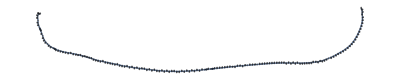

```mathematica
Graph@Select[graphPaths, MemberQ[shortestPath, #[[1]]]&]
```

### Debugging

```mathematica
connections =ConnectedComponents[newGraph]
```

{{{c,41,12},{c,40,12},{c,41,11},{c,41,13},{c,39,12},{c,40,11},{c,40,13},{c,41,10},{c,41,14},{c,38,12},{c,39,11},{c,39,13},{c,40,10},{c,40,14},{c,41,9},{c,38,11},{c,38,13},{c,39,10},{c,39,14},{c,40,9},4558,{r,19,131},{r,20,130},{r,17,132},{r,18,131},{r,18,133},{r,19,130},{r,17,133},{r,18,130},{r,18,134},{r,16,133},{r,17,134},{r,16,134},{r,17,135},{r,16,135},{r,17,136},{r,15,135},{r,16,136},{r,15,136},{r,16,137}},41,{1}}
 |  |  |  |

```mathematica
Length[#] & /@ connections
```

{4597,330,247,200,182,162,104,70,59,49,47,43,39,30,30,30,30,29,29,29,26,25,23,20,19,18,17,16,15,14,14,14,14,14,12,12,11,11,8,8,7,4,4}

```mathematica
MemberQ[#, endPos]&/@ connections
MemberQ[#, startPos]&/@ connections
```

{False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
newGraphPaths[[1]]
```

{a,1,1}<->{b,1,2}

```mathematica
connections[[1]]//Last
```

{r,16,137}

```mathematica
graph1=Select[newGraphPaths, MemberQ[connections[[1]], #[[1]]]&];
Graph[graph1]
```

```mathematica
Length[connections]
```

45

```mathematica
shortestFunc[endPos]
```

{}

```mathematica
HighlightGraph[graph,PathGraph[shortestPath]]
```

## From Arbitrary Start of Height a

### Test Data

```mathematica
posToValueTest//Length
```

40

```mathematica
possibleStartingPointsTest = Select[posToValueTest, MatchQ[#,"S" |"a"]&];
possibleStartingPointsTest//Length
```

6

```mathematica
possibleStartingPointsTest
```

<|{1,1}→S,{1,2}→a,{2,1}→a,{3,1}→a,{4,1}→a,{5,1}→a|>

```mathematica
possibleStartingPointsTest = Function[
{#[[2]], Sequence@@#[[1]]}
] /@ Normal[possibleStartingPointsTest];
```

```mathematica
posStartToLengthsTest =Association@@Function[
# -> Length[FindShortestPath[graphTest,#, endPosTest]]
] /@possibleStartingPointsTest
```

<|{S,1,1}→32,{a,1,2}→31,{a,2,1}→31,{a,3,1}→32,{a,4,1}→31,{a,5,1}→30|>

```mathematica
Select[posStartToLengthsTest, # >0 &]//Length
```

6

```mathematica
Values[Select[posStartToLengthsTest, # >0 &]]//Min
```

30

### Real

```mathematica
posToValue//Length
```

6683

```mathematica
possibleStartingPoints = Select[posToValue, MatchQ[#,"S" |"a"]&];
possibleStartingPoints//Length
```

2065

```mathematica
possibleStartingPoints
```

<|{1,1}→a,{1,7}→a,{1,8}→a,{1,9}→a,{1,10}→a,{1,11}→a,{1,12}→a,{1,13}→a,{1,14}→a,{1,15}→a,{1,16}→a,{1,17}→a,{1,18}→a,{1,19}→a,{1,22}→a,{1,23}→a,{1,24}→a,{1,25}→a,{1,26}→a,{1,27}→a,{1,28}→a,2023,{41,75}→a,{41,77}→a,{41,78}→a,{41,88}→a,{41,89}→a,{41,90}→a,{41,97}→a,{41,98}→a,{41,99}→a,{41,101}→a,{41,102}→a,{41,109}→a,{41,110}→a,{41,111}→a,{41,112}→a,{41,158}→a,{41,159}→a,{41,160}→a,{41,161}→a,{41,162}→a,{41,163}→a|>
 |  |  |  |

```mathematica
possibleStartingPoints = Function[
{#[[2]], Sequence@@#[[1]]}
] /@ Normal[possibleStartingPoints];
```

```mathematica
possibleStartingPoints[[1;;2]]
```

{{a,1,1},{a,1,7}}

```mathematica
Length[{555,571,570,569,568,567,566,565,566,567,568,569,570,571,580,579,580,581,582,583,584,585,603,602,603,604,605,606,607,608,0,0}]
```

32

```mathematica
posStartToLengths =Association@@Function[
# -> Length[FindShortestPath[graph,#, endPos]]
] /@possibleStartingPoints
```

<|{a,1,1}→555,{a,1,7}→571,{a,1,8}→570,{a,1,9}→569,{a,1,10}→568,{a,1,11}→567,{a,1,12}→566,{a,1,13}→565,{a,1,14}→566,{a,1,15}→567,{a,1,16}→568,{a,1,17}→569,{a,1,18}→570,{a,1,19}→571,{a,1,22}→580,{a,1,23}→579,{a,1,24}→580,2032,{a,41,90}→0,{a,41,97}→0,{a,41,98}→0,{a,41,99}→0,{a,41,101}→0,{a,41,102}→0,{a,41,109}→0,{a,41,110}→0,{a,41,111}→0,{a,41,112}→0,{a,41,158}→0,{a,41,159}→0,{a,41,160}→0,{a,41,161}→0,{a,41,162}→0,{a,41,163}→0|>
 |  |  |  |

```mathematica
Select[posStartToLengths, # >0 &]//Length
```

424

```mathematica
Values[Select[posStartToLengths, # >0 &]]//Min
```

526